### p=2

```mathematica
$Assumptions={Mp>0,C[1]>0,C[2]>0,α>0,β>0,ϵ>0};
```

```mathematica
Xsol[NN_]=X[NN]/.DSolve[-6 X'[NN]/X[NN]-2 X''[NN]/X'[NN]==2/NN,X[NN],NN][[1]]/.{C[2]->C[2] Mp^4}//Simplify
```

Mp^4 C[2] (C[1]+4 Log[NN])^(1/4)

```mathematica
Psol[NN_]=3/(2 Mp^4)β/α Xsol[NN]^2
```

(3 Mp^4 β C[2]^2 √(C[1]+4 Log[NN]))/(2 α)

```mathematica
phiN[NN_]=-Sqrt[(3 Mp^2 Xsol[NN])/Psol[NN]]//Simplify
```

-(√2 Mp √(α/(β C[2])))/(C[1]+4 Log[NN])^(1/8)

```mathematica
priphi[NN_]=Simplify[Integrate[phiN[NN],NN],{4Log[NN]+C[1]>0}]
```

-(-1)^(1/8) 2^(1/4) ⅇ^(-C[1]/4) Mp √(α/(β C[2])) Gamma[7/8,-C[1]/4-Log[NN]]

```mathematica
InverseFunction[priphi][f]
```

priphi^(-1)[f]

```mathematica
Simplify[Normal[Series[Gamma[7/8,-1/ϵ],{ϵ,0,1}]],{ϵ>0}]
```

-(-1)^(7/8) ⅇ^(1/ϵ) ϵ^(1/8)

```mathematica
priphi[Exp[1/ϵ-C[1]/4]]//Simplify
```

-(-1)^(1/8) 2^(1/4) ⅇ^(-C[1]/4) Mp √(α/(β C[2])) Gamma[7/8,-1/ϵ]

```mathematica
priphiasym[NN_]=Normal[Series[priphi[Exp[1/ϵ-C[1]/4]]//Simplify,{ϵ,0,1}]]/.{ϵ->1/(Log[NN]+C[1]/4)}//Simplify
```

-√2 Mp NN √(α/(β C[2])) (1/(C[1]+4 Log[NN]))^(1/8)

```mathematica
phi[NN_]=priphi[NN]-Sqrt[2]Mp Sqrt[α/(β C[2])]C[3]//Simplify
```

-2^(1/4) ⅇ^(-C[1]/4) Mp √(α/(β C[2])) (2^(1/4) ⅇ^(C[1]/4) C[3]+(-1)^(1/8) Gamma[7/8,-C[1]/4-Log[NN]])

```mathematica
phi[NN]/(Sqrt[2]Mp Sqrt[α/(β C[2])])//Simplify
```

-C[3]-((-1)^(1/8) ⅇ^(-C[1]/4) Gamma[7/8,-C[1]/4-Log[NN]])/2^(1/4)

```mathematica
phiasym[NN_]=Normal[Series[phi[Exp[1/ϵ-C[1]/4]]//Simplify,{ϵ,0,1}]]/.{ϵ->1/(Log[NN]+C[1]/4)}//Simplify
```

-√2 Mp √(α/(β C[2])) (C[3]+NN (1/(C[1]+4 Log[NN]))^(1/8))

```mathematica
InverseFunction[phiasym][x]
```

phiasym^(-1)[x]

```mathematica
InverseFunction[#(Log[#])^(-1/8)&][x]
```

InverseFunction[#1 Log[#1]^(-1/8)&][x]

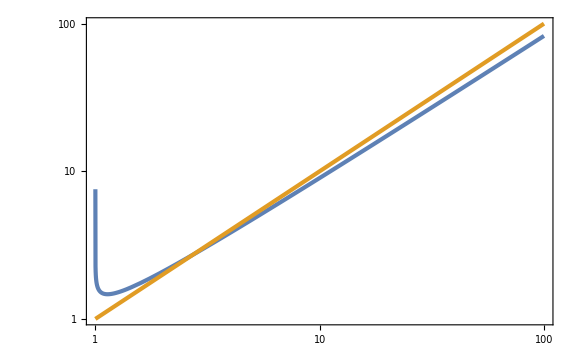

```mathematica
LogLogPlot[{x/Log[x]^(1/8),x},{x,1,100}]
```

### p!=2

```mathematica
Quit
```

```mathematica
$Assumptions={Mp>0,C[1]>0,C[2]>0,α>0,β>0,ϵ>0};
```

```mathematica
Xsol[NN_]=X[NN]/.DSolve[-6 X'[NN]/X[NN]-2 X''[NN]/X'[NN]==p/NN,X[NN],NN][[1]]/.{C[1]->C[1]/(2-p),C[2]->C[2] Mp^4}//Simplify
```

Mp^4 (8 NN^(1-p/2)+C[1])^(1/4) C[2]

```mathematica
Psol[NN_]=3/(2 Mp^4)β/α Xsol[NN]^2//Simplify
```

(3 Mp^4 β √(8 NN^(1-p/2)+C[1]) C[2]^2)/(2 α)

```mathematica
phiN[NN_]=-Sqrt[(3 Mp^2 Xsol[NN])/Psol[NN]]//Simplify
```

-(√2 Mp √(α/(β C[2])))/((8 NN^(1-p/2)+C[1])^(1/8))

```mathematica
priphi[NN_]=Integrate[phiN[NN],NN]//Simplify
```

-(√2 Mp NN √(α/(β C[2])) Hypergeometric2F1[1/8,-2/(-2+p),(-4+p)/(-2+p),-(8 NN^(1-p/2))/C[1]])/C[1]^(1/8)

```mathematica
InverseFunction[priphi][f]
```

priphi^(-1)[f]

```mathematica
phi[NN_]=priphi[NN]-Sqrt[2]Mp Sqrt[α/(β C[2])]C[3]//Simplify
```

-(√2 Mp √(α/(β C[2])) (C[1]^(1/8) C[3]+NN Hypergeometric2F1[1/8,-2/(-2+p),(-4+p)/(-2+p),-(8 NN^(1-p/2))/C[1]]))/C[1]^(1/8)

#### p<2

```mathematica
Normal[Series[phi[NN],{NN,∞,0},Assumptions->{0<p<2}]]//Simplify
```

2^(1/8) Mp √(α/(β C[2])) ((8 NN^((14+p)/16) (-2+p) Gamma[(-4+p)/(-2+p)])/((14+p) Gamma[-2/(-2+p)])+2^(3/8) (-C[3]-(2^(6/(-2+p)) C[1]^((14+p)/(16-8 p)) Gamma[1/8+2/(-2+p)] Gamma[(-4+p)/(-2+p)])/Gamma[1/8]))

```mathematica
phiasym[NN_]=2^(1/8) Mp √(α/(β C[2])) (8 NN^((14+p)/16) (-2+p) Gamma[(-4+p)/(-2+p)])/((14+p) Gamma[-2/(-2+p)])//FullSimplify
```

-(16 2^(1/8) Mp NN^((14+p)/16) √(α/(β C[2])))/(14+p)

```mathematica
phiasym[NN]/(Sqrt[2/C[2]]Mp Sqrt[α/β])//Simplify
```

-(8 2^(5/8) NN^((14+p)/16))/(14+p)

```mathematica
Nasym[x_]=InverseFunction[phiasym][x]//Simplify
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

2^(-66/(14+p)) (-((14+p) x)/(Mp √(α/(β C[2]))))^(16/(14+p))

```mathematica
(1/2+3+5/8)16/(p+14)
```

66/(14+p)

```mathematica
Xsol[NN]
```

Mp^4 (8 NN^(1-p/2)+C[1])^(1/4) C[2]

```mathematica
Xasym[x_]=Simplify[Mp^4 (8 Nasym[x]^(1-p/2))^(1/4) C[2]/2,{0<p<2}]
```

(Mp^4 (2^(-66/(14+p)) (-((14+p) x)/(Mp √(α/(β C[2]))))^(16/(14+p)))^((2-p)/8) C[2])/2^(1/4)

```mathematica
-1/4-(1/2+3+5/8)(2(2-p))/(p+14)//Simplify
```

(4 (-5+2 p))/(14+p)

```mathematica
1/2-(1/2+3+5/8)(4(2-p))/(p+14)//Simplify
```

(-26+17 p)/(14+p)

```mathematica
2+(2(2-p))/(p+14)//Simplify
```

32/(14+p)

```mathematica
1+(2(2-p))/(p+14)//Simplify
```

(18-p)/(14+p)

#### p>2

```mathematica
Normal[Series[priphi[NN],{NN,∞,0},Assumptions->{p>2}]]//Simplify
```

(Mp NN (9 NN^(2-p) (-4+p)-4 NN^(1-p/2) (-3+p) C[1]-2 (12-7 p+p^2) C[1]^2))/(√2 (-4+p) (-3+p) C[1]^(17/8) √((β C[2])/α))

```mathematica
phiasym[NN_]=(Mp NN (-2 (12-7 p+p^2) C[1]^2))/(√2 (-4+p) (-3+p) C[1]^(17/8) √((β C[2])/α))//FullSimplify
```

-(√2 Mp NN)/(C[1]^(1/8) √((β C[2])/α))

```mathematica
2+1/2(p-2)/2//Simplify
```

(6+p)/4

```mathematica
-1-1/8(p-2)/2//Simplify
```

-7/8-p/16